```mathematica
SetDirectory["C:/Users/MaeLSTRoM/Desktop/Coding/ant/data/sleap"]
```

C:\Users\MaeLSTRoM\Desktop\Coding\ant\data\sleap

```mathematica
file=Import["testset.hdf5","Data"];
```

```mathematica
src=file⟦"/trajectory_0"⟧;
```

```mathematica
list={};
Do[
src=file⟦n+Length[file]/2⟧;
frames=file⟦n⟧;
head=src⟦;;,1⟧;
thorax=src⟦;;,2⟧;
abdomen=src⟦;;,3⟧;
Do[
If[head⟦1,m⟧>1,
(*skip*),
head⟦1,m⟧=head⟦1,m-1⟧;
];
If[head⟦2,m⟧>1,
(*skip*),
head⟦2,m⟧=head⟦2,m-1⟧
]
,{m,1,Length[head⟦1⟧]}];
Do[
If[thorax⟦1,m⟧>1,
(*skip*),
thorax⟦1,m⟧=thorax⟦1,m-1⟧;
];
If[thorax⟦2,m⟧>1,
(*skip*),
thorax⟦2,m⟧=thorax⟦2,m-1⟧
]
,{m,1,Length[thorax⟦1⟧]}];
Do[
If[abdomen⟦1,m⟧>1,
(*skip*),
abdomen⟦1,m⟧=abdomen⟦1,m-1⟧;
];
If[abdomen⟦2,n⟧>1,
(*skip*),
abdomen⟦2,m⟧=abdomen⟦2,m-1⟧
]
,{m,1,Length[abdomen⟦1⟧]}];
avg=(head+thorax+abdomen)/3.;
AppendTo[list,avgᵀ];

(*Length[file] is always an even number, because the converter creates one table for trajectory and one table for frame numbers for every SLEAP trajectory in the input file.*)
,{n,1,Length[file]/2}]
```

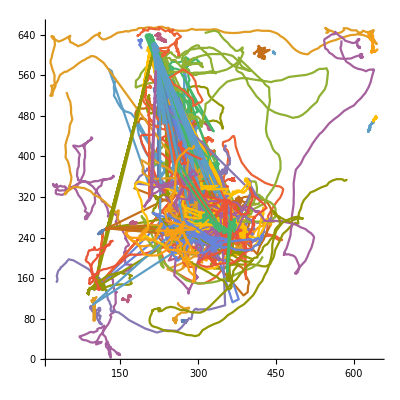

```mathematica
ListPlot[list⟦;;⟧,PlotRange->All,Joined->True,ImageSize->Full,AspectRatio->1]
```

```mathematica
list=list[[1;;2]];
```

## Jump counts/disconnect trajectories

```mathematica
Module[{jump,θ=15.1},
ct=0;
pruned={};
Do[
jump=1;
sc=0;
Do[
If[
Norm[list⟦i,j⟧-list⟦i,j-1⟧]>θ,
AppendTo[pruned,list⟦i,jump;;j-1⟧];
jump=j;
sc+=1;
ct+=1];
,{j,2,Length[list⟦i⟧]}];
If[sc==0,
AppendTo[pruned,list⟦i⟧];
ct+=1],
{i,1,Length[list]}]
];
```

```mathematica
Length[list[[1]]]
```

492

```mathematica
sc
```

9

```mathematica
ct
```

663

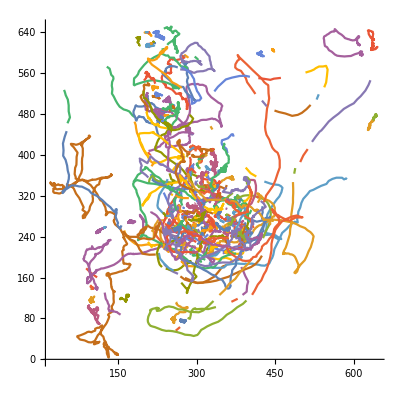

```mathematica
ListPlot[pruned⟦;;⟧,PlotRange->All,Joined->True,ImageSize->Full,AspectRatio->1]
```

## Compute predicted position

```mathematica
Module[{
ω,speed,vec,dir,arg,
refrange=5(*Number of frames to refer to for finding potential next position*)
},
prediction={};
Do[
If[Length[pruned⟦n⟧]>refrange,
(*Sufficiently long trajectories*)
ω=0;
speed=0;
vec=0;
Do[
j=refrange+1-i;
vec=pruned⟦n,-j⟧-pruned⟦n,-j-1⟧;
speed+=Abs[vec];
dir=vec/(Abs[vec]+0.000000000001);
arg=dir⟦1⟧/dir⟦2⟧;
If[dir⟦2⟧≥0,
ω+=ArcTan[arg],
ω+=1.π+ArcTan[arg];
];
,{i,1,refrange}];
speed=speed/refrange;
ω=ω/refrange;
,
(*Too short to establish good prediction*)
speed=0;
ω=0;
];
AppendTo[prediction,{pruned⟦n,-1⟧,pruned⟦n,-1⟧+speed{Cos[ω],Sin[ω]}}];
,{n,1,Length[pruned]}];
]
```

```mathematica
Module[{
ω,speed,vec,
refrange=6(*Number of frames to refer to for finding potential next position*)
},
Do[
If[Length[pruned⟦n⟧]>refrange+1,
(*Sufficiently long trajectories*)
ω=0;
speed=0;
vec=0;
Do[
vec=pruned⟦n,i+1⟧-pruned⟦n,i⟧;
speed+=Abs[vec];
ω+=vec/(Abs[vec]+0.000000000001)
,{i,1,refrange}];
speed=speed/refrange;
ω=ω/refrange;
,
(*Too short to establish good prediction*)
speed=0;
ω=0;
];
AppendTo[prediction,{pruned⟦n,1⟧,pruned⟦n,1⟧-speed ω}];
,{n,1,Length[pruned]}]
]
```

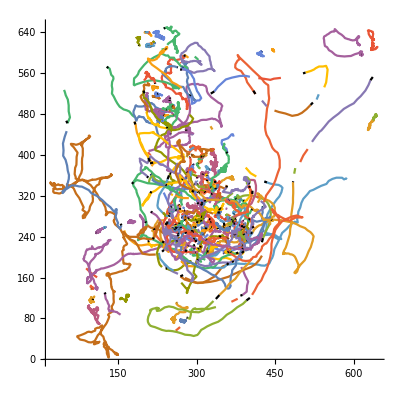

```mathematica
Show[ListPlot[pruned⟦;;⟧,PlotRange->All,Joined->True,ImageSize->Full,AspectRatio->1],ListPlot[prediction⟦;;⟧,Joined->True,PlotStyle->Black]]
```

```mathematica
-
```

```mathematica
prediction
```

{{{279.238,76.2332},{279.238+0.0794006 Cos[1/5 (3.14159+ArcTan[(-1.)⟦1⟧]+ArcTan[(-1.)⟦1⟧]+ArcTan[1.⟦1⟧]+ArcTan[1.⟦1⟧]+ArcTan[1.⟦1⟧])],76.2332+0.200003 Sin[1/5 (3.14159+ArcTan[(-1.)⟦1⟧]+ArcTan[(-1.)⟦1⟧]+ArcTan[1.⟦1⟧]+ArcTan[1.⟦1⟧]+ArcTan[1.⟦1⟧])]}},661,{{371.08,276.976},{371.08,276.976}}}
 |  |  |  |